```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\shiyi\work\git\work\factorial_cumulant\fRG-QM\v2\finitemub

## Import data

```mathematica
l=13;
chi1PQMP=Table[Flatten[Import["./mub"<>ToString[(i-1)*50]<>"/final/buffer/chi1.dat"]],{i,1,l}];
chi2PQMP=Table[Flatten[Import["./mub"<>ToString[(i-1)*50]<>"/final/buffer/chi2.dat"]],{i,1,l}];
chi3PQMP=Table[Flatten[Import["./mub"<>ToString[(i-1)*50]<>"/final/buffer/chi3.dat"]],{i,1,l}];
chi4PQMP=Table[Flatten[Import["./mub"<>ToString[(i-1)*50]<>"/final/buffer/chi4.dat"]],{i,1,l}];
R21=chi2PQMP/chi1PQMP;
R42=chi4PQMP/chi2PQMP;
R41=chi4PQMP/chi1PQMP;
R31=chi3PQMP/chi1PQMP;
k1=chi1PQMP;
k2=chi2PQMP-chi1PQMP;
k3=2chi1PQMP-3chi2PQMP+chi3PQMP;
k4=-6 chi1PQMP+11chi2PQMP-6chi3PQMP+chi4PQMP;
Rf41=k4/k1;
Rf31=k3/k1;
```

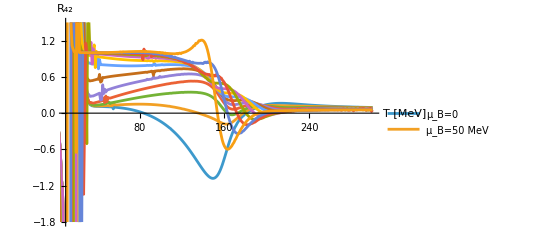

```mathematica
Plot1=ListLinePlot[R42,PlotLegends->{"μ_B=0","μ_B=50 MeV"},PlotRange->{{10,300},{-1.8,1.5}},AxesLabel->{"T [MeV]","R_42"}]
```

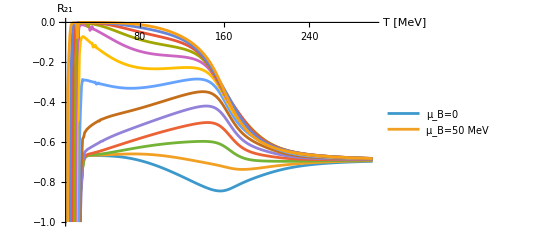

```mathematica
Plot21=ListLinePlot[R21-1,PlotStyle->{Automatic},PlotLegends->{"μ_B=0","μ_B=50 MeV"},PlotRange->{{10,300},{-1.,0}},AxesLabel->{"T [MeV]","R_21"}]
```

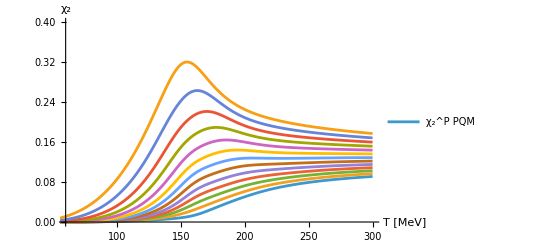

```mathematica
Plot2=ListLinePlot[chi2PQMP,PlotLegends->{"χ_2^P PQM"},PlotRange->{{60,300},{0,0.4}},AxesLabel->{"T [MeV]","χ_2"}]
```

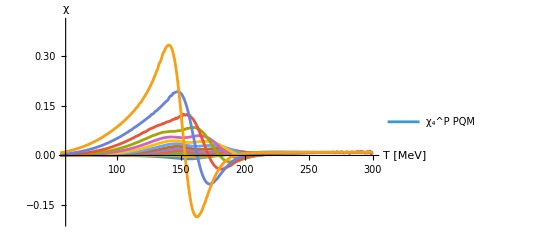

```mathematica
Plot3=ListLinePlot[chi4PQMP,PlotLegends->{"χ_4^P PQM"},PlotRange->{{60,300},{-0.2,0.4}},AxesLabel->{"T [MeV]","χ"}]
```

## freeze-out

```mathematica
T=Table[i,{i,1,300}];
```

```mathematica
sqrts=Table[1307.5/(0.288 mu)-1/0.288,{mu,50,600,50}]
```

{87.3264,41.9271,26.794,19.2274,14.6875,11.6609,9.49901,7.8776,6.61651,5.60764,4.7822,4.09433}

```mathematica
Tcf=158.4/(1+Exp[2.60-Log[sqrts]/0.45])
```

{158.296,157.873,156.982,155.465,153.139,149.806,145.257,139.296,131.77,122.612,111.88,99.8006}

```mathematica
r=1.15;
fit42=Table[Interpolation[Transpose[{T/r,R42[[i]]}],InterpolationOrder->1],{i,1,l}];
fit21=Table[Interpolation[Transpose[{T/r,R21[[i]]}],InterpolationOrder->1],{i,1,l}];
fitRf41=Table[Interpolation[Transpose[{T/r,Rf41[[i]]}],InterpolationOrder->1],{i,1,l}];
fitRf31=Table[Interpolation[Transpose[{T/r,Rf31[[i]]}],InterpolationOrder->1],{i,1,l}];
```

```mathematica
R42cf=Table[fit42[[i+1]][Tcf[[i]]],{i,1,l-1}];
R21cf=Table[fit21[[i+1]][Tcf[[i]]],{i,1,l-1}];
Rf41cf=Table[fitRf41[[i+1]][Tcf[[i]]],{i,1,l-1}];
Rf31cf=Table[fitRf31[[i+1]][Tcf[[i]]],{i,1,l-1}];
```

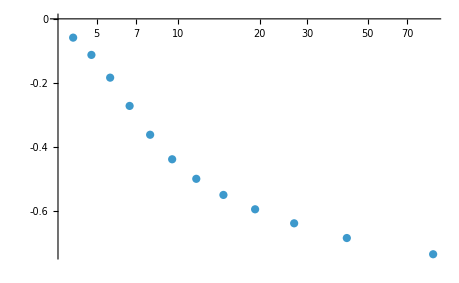

```mathematica
ListPlot[{Transpose[{sqrts,R21cf-1}]},PlotRange->All,ScalingFunctions->{"Log","Linear"}]
```

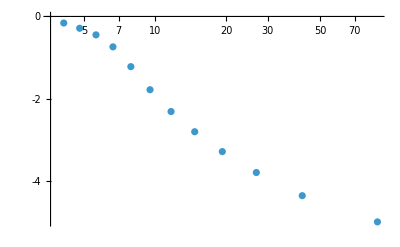

```mathematica
ListPlot[{Transpose[{sqrts,Rf41cf}]},PlotRange->{All,All},ScalingFunctions->{"Log","Linear"}]
```

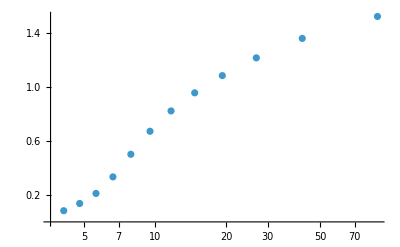

```mathematica
ListPlot[{Transpose[{sqrts,Rf31cf}]},PlotRange->{All,All},ScalingFunctions->{"Log","Linear"}]
```

```mathematica
Export["./R42.dat",Transpose[{sqrts,R42cf}]]
Export["./R41fac.dat",Transpose[{sqrts,Rf41cf}]]
Export["./R31fac.dat",Transpose[{sqrts,Rf31cf}]]
Export["./R21fac.dat",Transpose[{sqrts,R21cf-1}]]
```

./R42.dat

./R41fac.dat

./R31fac.dat

./R21fac.dat